#### Функция одной переменной

```mathematica
f[x_]:=3 x^2
```

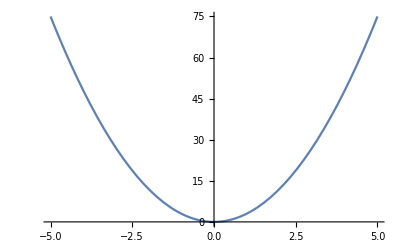

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
df[x_]:=6x
```

```mathematica
x0=5;
λ=0.1;
```

```mathematica
res={};
```

```mathematica
While[
AppendTo[res,{x0,f[x0]}];
x1=x0-λ df[x0];
Norm[{x0-x1}]>0.00000001,
x0=x1
]
```

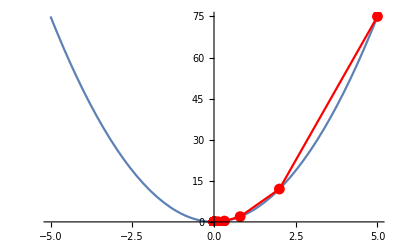

```mathematica
Show[
Plot[f[x],{x,-5,5}],
ListLinePlot[res,Mesh->All,PlotStyle->Red,PlotRange->All]
]
```

#### Функция двух переменной

```mathematica
f[x_,y_]:=3 x^2+5 y^2
```

```mathematica
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
df[x_,y_]:={6x,10y}
```

```mathematica
x0={5,10};
λ=0.1;
```

```mathematica
res={};
```

```mathematica
While[
AppendTo[res,Append[x0,f@@x0]];
x1=x0-λ df@@x0;
Norm[x1-x0]>0.00000001,
x0=x1
]
```

```mathematica
(x0-x1)^2
```

{2.78537×10^-17,0.}

```mathematica
Show[
Plot3D[f[x,y],{x,-5,5},{y,-5,5}],
ListLinePlot3D[res,Mesh->All,PlotStyle->Blue,PlotRange->All]
]
```

-Graphics3D-

#### Домашнее задание

Реализовать в python метод градиентного спуска для одной и двух переменных, как в примерах выше. Для примера 1 построить график сходимости. 
Реализовать метод наискорейшего спуска в python или WM.